# Script for IRS vs BoB comparison 1:1 Mass ratio

## to accompany https://arxiv.org/abs/2203.08998

Author: Maria Babiuc-Hamilton and Dillon Buskirk

```mathematica
ClearAll["Global`*"];Off[General::spell];Remove["Global`*"]
SetOptions[Simplify,TimeConstraint->1000];
$Assumptions=η>0 &&t∈Reals;
Unprotect[Sqrt]; Sqrt[x_^2]:=x; Protect[Sqrt];
$MinPrecision=20; (* $MachinePrecision;*)
```

Initial and final parameters

From FinalSpinMassQNM.nb,  values for equal non-spinning binaries χf0Meq and Mfχ0Meq

```mathematica
χf=0.686526691452522(*nonspinning individual BSs in the binary *)
```

0.686527

```mathematica
Mf=0.95158896875;
```

We take the mean value for equal non-spinning binaries from FinalSpinMassQNM.nb,  for l=2, m=2 mode:

```mathematica
MfωQNM = 0.5422370151014632;
QQNM=3.300909722911351;
ωQNM=MfωQNM/Mf
τ = 2 QQNM/ωQNM
```

0.569823

11.5857

Freely chosen parameters

```mathematica
Ap=1;R=1;tp=0;
```

Starting BOB formulation

```mathematica
Ωisco=(-0.091933*χf+0.097593)/(χf^2-2.4228*χf+1.4366)
ωqnm=1.5251-1.1568*(1-χf)^0.1292
```

0.140958

0.529311

take the initial values from the inspiral for ti = tLR

Values taken directly from EccInsMerger_q1e0001. For this spin, rISCO=3.45425.

```mathematica
e3PNISCO =1.30569 10^-4;
x3PNISCO =0.178329;
Ω3OrbPNISCO = 0.075297 ;
Ω3PN =2 Ω3OrbPNISCO;
r3PNISCO = 4.83849;
Ω3OrbPNISCOdot = 8.57723 10^-4 ;
Ω3PNdot =2Ω3OrbPNISCOdot;
```

Now we can implement the BoB

```mathematica
Ωi = Ω3OrbPNISCO (*Ωisco*) ;
Ωidot = Ω3OrbPNISCOdot;
tp =0;
ΩQNM=ωQNM/2;
ti=tp-τ/2 Log[(ΩQNM^4-Ωi^4)/(2*τ*Ωi^3 Ωidot)-1]
```

-38.5154

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

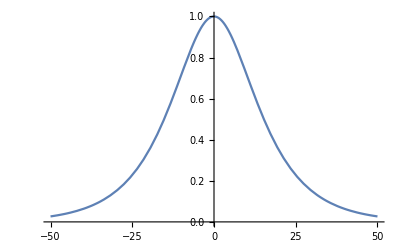

```mathematica
Ap=1;(*1.068*(1-Mf)^0.8918;*)
ψ4[t_]:=Ap*Sech[(t-tp)/τ];
Plot[ψ4[t],{t,-50,50}]
```

```mathematica
kB=((ΩQNM^4-Ωi^4)/(1-Tanh[(ti-tp)/τ]))
```

0.00328282

```mathematica
ΩB[t_]:=(Ωi^4+kB(Tanh[(t-tp)/τ]-Tanh[(ti-tp)/τ]))^(1/4)
```

```mathematica
ωBoB[t_]:=2*ΩB[t];
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

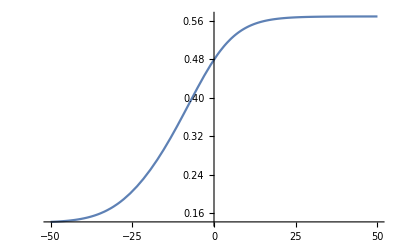

```mathematica
Plot[ωBoB[t],{t,-50,50}]
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

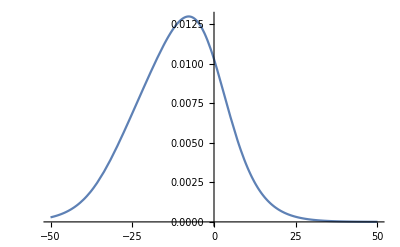

```mathematica
Plot[ωBoB'[t],{t,-50,50}]
```

```mathematica
Kappap=(Ωi^4+kB(1-Tanh[(ti-tp)/τ]))^(1/4)
```

0.284911

```mathematica
Kappam=(Ωi^4-kB(1+Tanh[(ti-tp)/τ]))^(1/4)
```

0.0697355

```mathematica
arctanp[t_]:=Kappap*τ*(ArcTan[(ΩB[t]/Kappap)]-ArcTan[Ωi/Kappap])
arctanm[t_]:=Kappam*τ*(ArcTan[ΩB[t]/Kappam]-ArcTan[Ωi/Kappam])
arctanhp[t_]:=Kappap*τ*(ArcTanh[ΩB[t]/Kappap]-ArcTanh[Ωi/Kappap])
arctanhm[t_]:=Kappam*τ*(ArcTanh[ΩB[t]/Kappam]-ArcTanh[Ωi/Kappam])
```

```mathematica
PhaseB[t_]:=arctanp[t]+arctanhp[t]-arctanm[t]-arctanhm[t]
```

```mathematica
ϕBoB[t_]:=2*PhaseB[t]
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

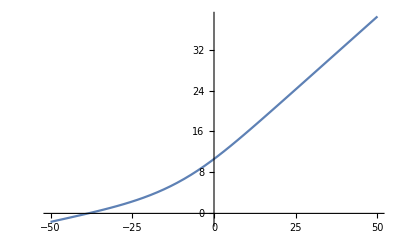

```mathematica
Plot[ϕBoB[t],{t,-50,50}]
```

```mathematica
AmpBoB[t_]:=ψ4[t]/ωBoB[t]^2
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

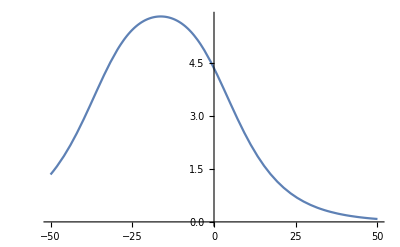

```mathematica
Plot[AmpBoB[t],{t,-50,50}]
```

```mathematica
hBoB[t_]:=AmpBoB[t]*Exp[-ⅈ* ϕBoB[t]]
```

```mathematica
FindMaximum[AmpBoB[t],t]
```

{5.81142,{t→-16.3066}}

```mathematica
t0BoB=-16.30656956691866;
```

```mathematica
MaxAmpBoB=MaxValue[AmpBoB[t],t]
```

5.81142

```mathematica
FindRoot[AmpBoB'[t]==0,{t,-40,40}]
```

{t→-16.3066}

Note that the maximum in amplitude and maximum in the rate of variation of the frequency is not the same!

```mathematica
FindRoot[ωBoB''[t]==0,{t,-40,0}]
```

{t→-7.74222}

```mathematica
tfBoB=-7.742219427214392;
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

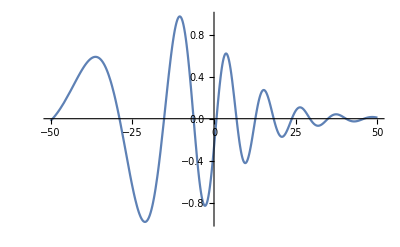

```mathematica
Plot[Re[hBoB[t]]/MaxAmpBoB,{t,-50,50}]
```

Now we implement the IRS

```mathematica
m1 =0.5; m2=1-m1;
q=m1/m2; M=m1+m2; μ=(m1*m2)/M;η=μ/M;
```

Check the initial frequency, quality factor and damping time against the numerical fit

```mathematica
sfn=2*(3)^(1/2)η-390/79 η^2+2379/287 η^3-4621/276 η^4;
ωqm=1-0.63(1-sfn)^0.3;
```

```mathematica
ScientificForm[MeanDeviation[{ωqm,ωQNM}]]
```

2.02517×10^-2

```mathematica
Q=2/(1-sfn)^0.45;
```

```mathematica
ScientificForm[MeanDeviation[{Q,QQNM}]]
```

1.01919×10^-1

1107.1181 takes b = τ

```mathematica
b=N[16014/979-29132/1343 η^2];
```

```mathematica
ScientificForm[MeanDeviation[{b,τ}]]
```

1.70802

Will use τ for consistency

```mathematica
c=N[206/903+180/1141 η^(1/2)+424/1205*η^2/Log[η]];
kI=N[713/1056-23/193 η];
α=N[1/QQNM^2(16313/562+21345/124 η)];
```

```mathematica
fs[t_]:=c/2(1+1/kI)^(1+kI)(1-(1+1/kI ⅇ^((-2*t)/τ))^-kI);
fs2=Simplify[fs[t]^2, Assumptions->{η>0}];fs4=Simplify[fs2^2];
fsdot=Simplify[D[fs[t],t]];
```

```mathematica
ωIRS[t_]:=ωQNM*(1-fs[t])
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

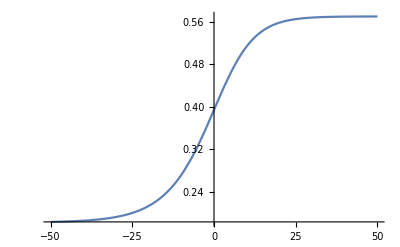

```mathematica
Plot[ωIRS[t],{t,-50,50}]
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

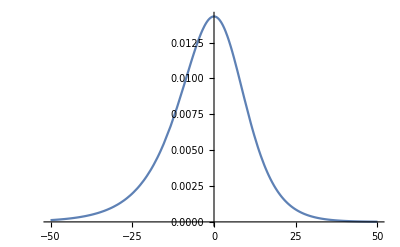

```mathematica
Plot[ωIRS'[t],{t,-50,50}]
```

```mathematica
FindRoot[ωIRS''[t]==0,{t,-40,40}]
```

{t→-3.39233×10^-15}

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of SetPrecision::precsm will be suppressed during this calculation.

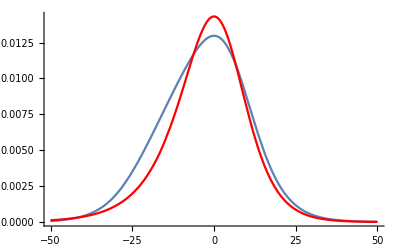

```mathematica
Show[Plot[ωBoB'[t+tfBoB],{t,-50,50}],
Plot[ωIRS'[t],{t,-50,50},PlotStyle->Red], Axes->True,AxesOrigin->Automatic, PlotRange->{0,All}]
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of SetPrecision::precsm will be suppressed during this calculation.

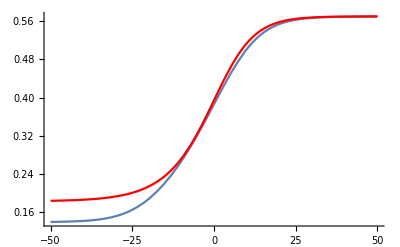

```mathematica
Show[Plot[ωBoB[t+tfBoB],{t,-50,50}],
Plot[ωIRS[t],{t,-50,50},PlotStyle->Red], Axes->True,AxesOrigin->Automatic, PlotRange->{0,All}]
```

```mathematica
ϕIRS= Integrate[ωIRS[t],t];
```

```mathematica
Δϕ= Re[ϕBoB[tfBoB]] - Simplify[ϕIRS/.{t->0}]
```

4.97002

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of SetPrecision::precsm will be suppressed during this calculation.

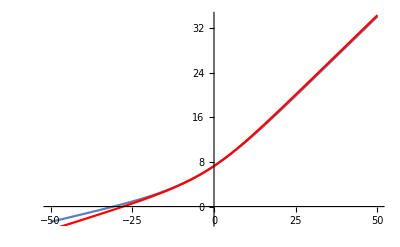

```mathematica
Show[Plot[ϕBoB[t+tfBoB],{t,-50,50}],
Plot[ϕIRS+Δϕ,{t,-50,50},PlotStyle->Red]]
```

```mathematica
AmpIRS[t_]:=Simplify[Ap/ωIRS[t](Abs[fsdot]/(1+α*(fs2-fs4)))^(1/2)]
```

```mathematica
MaxAmpIRS=MaxValue[AmpIRS[t],t]
```

0.325076

```mathematica
hIRS[t_]:=AmpIRS[t]*Exp[-ⅈ*(ϕIRS)]
```

```mathematica
hIRSΔ[t_]:=AmpIRS[t]*Exp[-ⅈ*(ϕIRS+Δϕ)]
```

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

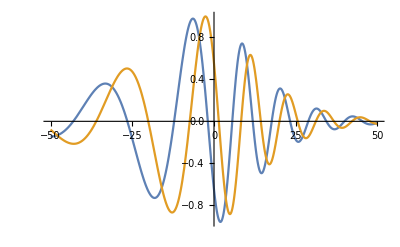

```mathematica
Plot[{Re[hIRS[t]]/MaxAmpIRS,Re[hIRSΔ[t]]/MaxAmpIRS},{t,-50,50}]
```

```mathematica
FindMinimum[{Re[hBoB[t]],-40<=t<=0},{t,-20}]
```

$MinPrecision::preccon: Cannot set $MinPrecision such that $MaxPrecision < $MinPrecision.

{-5.69835,{t→-21.1095}}

```mathematica
thBoBm=-21.109547744713712
```

-21.1095

```mathematica
FindMaximum[{Re[hBoB[t]],-40<=t<=0},{t,-10}]
```

$MinPrecision::preccon: Cannot set $MinPrecision such that $MaxPrecision < $MinPrecision.

{5.64543,{t→-10.4754}}

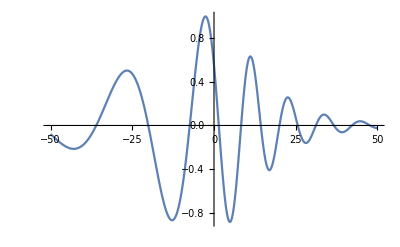

```mathematica
Plot[Re[hIRSΔ[t]]/MaxAmpIRS,{t,-50,50}]
```

```mathematica
FindMaximum[{Re[hIRS[t]]/MaxAmpIRS,-40<=t<=0},{t,-10}]
```

$MinPrecision::preccon: Cannot set $MinPrecision such that $MaxPrecision < $MinPrecision.

{0.979141,{t→-6.45085}}

```mathematica
thIRSp=-6.450848835030723
```

-6.45085

```mathematica
FindMinimum[{Re[hIRS[t]]/MaxAmpIRS,-40<=t<=10},{t,5}]
```

$MinPrecision::preccon: Cannot set $MinPrecision such that $MaxPrecision < $MinPrecision.

{-0.959004,{t→1.97114}}

```mathematica
FindMaximum[{Re[hIRSΔ[t]]/MaxAmpIRS,-40<=t<=0},{t,-5}]
```

$MinPrecision::preccon: Cannot set $MinPrecision such that $MaxPrecision < $MinPrecision.

{0.999993,{t→-2.60283}}

```mathematica
thIRSΔp=-2.60283032687171
```

-2.60283

```mathematica
FindMinimum[{Re[hIRSΔ[t]]/MaxAmpIRS,-40<=t<=0},{t,-15}]
```

$MinPrecision::preccon: Cannot set $MinPrecision such that $MaxPrecision < $MinPrecision.

{-0.869105,{t→-12.8144}}

```mathematica
FindMinimum[{Re[hIRSΔ[t]]/MaxAmpIRS,-10<=t<=20},{t, 5}]
```

$MinPrecision::preccon: Cannot set $MinPrecision such that $MaxPrecision < $MinPrecision.

{-0.884451,{t→4.8698}}

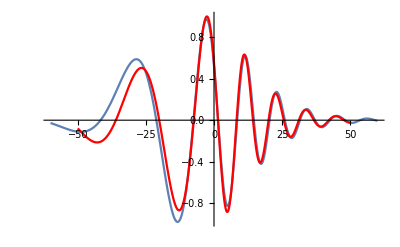

```mathematica
Show[Plot[Re[hBoB[t+tfBoB]]/MaxAmpBoB,{t,-60,60}],
Plot[Re[hIRSΔ[t]]/MaxAmpIRS,{t,-50,50},PlotStyle->Red],PlotRange->All]
```

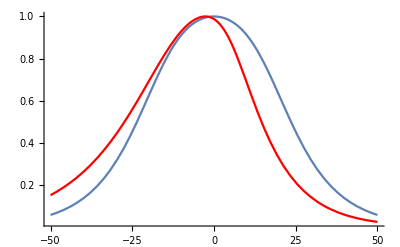

```mathematica
Show[Plot[AmpBoB[t+t0BoB]/MaxAmpBoB,{t,-50,50}],
Plot[AmpIRS[t]/MaxAmpIRS,{t,-50,50},PlotStyle->Red],PlotRange->All]
```

```mathematica
FindMaximum[AmpIRS[t],t]
```

{0.325076,{t→-2.6692}}

```mathematica
t0IRS=-2.6691980431766877
```

-2.6692

```mathematica
Δt0 = t0IRS-t0BoB
```

13.6374

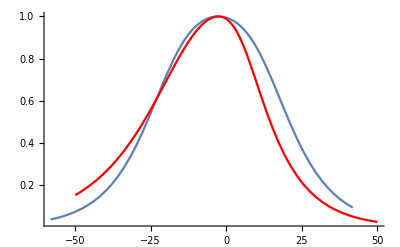

```mathematica
Show[Plot[AmpBoB[t-Δt0]/MaxAmpBoB,{t,-50+t0BoB/2,50+t0BoB/2}],
Plot[AmpIRS[t]/MaxAmpIRS,{t,-50,50},PlotStyle->Red],PlotRange->All]
```

Plots for the paper:

New plot for paper: phase for IRS-BoB comparison

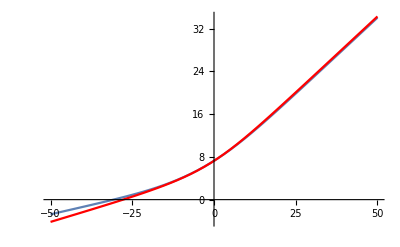

```mathematica
Show[Plot[ϕBoB[t+tfBoB],{t,-50,50}],
Plot[ϕIRS+Δϕ,{t,-50,50},PlotStyle->Red],PlotRange->All]
```

For the standard deviation plot

```mathematica
Show[Plot[Re[hBoB[t+tfBoB]]/MaxAmpBoB,{t,-60,60}],
Plot[Re[hIRSΔ[t]]/MaxAmpIRS,{t,-50,50},PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
(*dataBoBr=Re[hBoB[t-trBoB/2]]/MaxAmpBoB;
dataBoB0=Re[hBoB[t-Δt0/2]]/MaxAmpBoB;
dataIRS=Re[hIRSΔ[t]]/MaxAmpIRS;
datamIRS=Re[-hIRS[t]]/MaxAmpIRS;
datamIRSΔ=Re[-hIRSΔ[t]]/MaxAmpIRS;*)
```

## Below is Tabulating for Python Plots

```mathematica
dt=0.01;
```

```mathematica
tArray=Table[t,{t,-50,50,dt}];
```

```mathematica
(*ωBoBTab=Table[ωBoB[t-Δtp/2],{t,-50,50,dt}];*)
```

```mathematica
(*ωIRSTab=Table[ωIRS[t],{t,-50,50,dt}];*)
```

```mathematica
(*ωBoBvsTimeTab=Partition[Riffle[tArray,ωBoBTab],2];*)
```

```mathematica
(*PrependTo[ωBoBvsTimeTab, {"t(M)", "ω(t)"}];*)
```

```mathematica
(*ωIRSvsTimeTab=Partition[Riffle[tArray,ωIRSTab],2];*)
```

```mathematica
(*PrependTo[ωIRSvsTimeTab, {"t(M)", "ω(t)"}];*)
```

```mathematica
ϕBoBTab=Table[ϕBoB[t+tfBoB],{t,-50,50,dt}];
```

```mathematica
ϕIRSTab=Table[ϕIRS+Δϕ,{t,-50,50,dt}];
```

```mathematica
ϕBoBvsTimeTab=Partition[Riffle[tArray,ϕBoBTab],2];
```

```mathematica
PrependTo[ϕBoBvsTimeTab, {"t(M)", "ϕ(t)"}];
```

```mathematica
ϕIRSvsTimeTab=Partition[Riffle[tArray,ϕIRSTab],2];
```

```mathematica
PrependTo[ϕIRSvsTimeTab, {"t(M)", "ϕ(t)"}];
```

```mathematica
hBoBTab=Table[Re[hBoB[t+tfBoB]]/MaxAmpBoB,{t,-50,50,dt}];
```

```mathematica
hIRSTab=Table[Re[hIRSΔ[t]]/MaxAmpIRS,{t,-50,50,dt}];
```

```mathematica
hBoBvsTimeTab=Partition[Riffle[tArray,hBoBTab],2];
```

```mathematica
PrependTo[hBoBvsTimeTab, {"t(M)", "h(t)"}];
```

```mathematica
hIRSvsTimeTab=Partition[Riffle[tArray,hIRSTab],2];
```

```mathematica
PrependTo[hIRSvsTimeTab, {"t(M)", "h(t)"}];
```

```mathematica
(*AmpBoBTab=Table[AmpBoB[t-Δtp]/MaxAmpBoB,{t,-50,50,dt}];*)
```

```mathematica
(*AmpIRSTab=Table[AmpIRS[t]/MaxAmpIRS,{t,-50,50,dt}];*)
```

```mathematica
(*AmpBoBvsTimeTab=Partition[Riffle[tArray,AmpBoBTab],2];*)
```

```mathematica
(*PrependTo[AmpBoBvsTimeTab, {"t(M)", "hAmp(t)"}];*)
```

```mathematica
(*AmpIRSvsTimeTab=Partition[Riffle[tArray,AmpIRSTab],2];*)
```

```mathematica
(*PrependTo[AmpIRSvsTimeTab, {"t(M)", "hAmp(t)"}];*)
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/wBoB.txt", ωBoBvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/wIRS.txt", ωIRSvsTimeTab]*)
```

```mathematica
Export["dropbox/dillon/paperplottingwork/phiBoB.txt", ϕBoBvsTimeTab]
```

dropbox/dillon/paperplottingwork/phiBoB.txt

```mathematica
Export["dropbox/dillon/paperplottingwork/phiIRS.txt", ϕIRSvsTimeTab]
```

dropbox/dillon/paperplottingwork/phiIRS.txt

```mathematica
(*Export["dropbox/dillon/paperplottingwork/phiIRSShifted.txt", ϕIRSShiftedvsTimeTab]*)
```

```mathematica
Export["dropbox/dillon/paperplottingwork/hBoB.txt", hBoBvsTimeTab]
```

dropbox/dillon/paperplottingwork/hBoB.txt

```mathematica
Export["dropbox/dillon/paperplottingwork/hIRS.txt", hIRSvsTimeTab]
```

dropbox/dillon/paperplottingwork/hIRS.txt

```mathematica
(*Export["dropbox/dillon/paperplottingwork/hBoBShifted.txt", hBoBShiftedvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/hIRSShifted.txt", hIRSShiftedvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/AmpBoB.txt", AmpBoBvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/AmpIRS.txt", AmpIRSvsTimeTab]*)
```